```mathematica
SetDirectory[NotebookDirectory[]];
<<EvolAlgorithm4PatternFormingGRCModel2MathPackageV9.m
<<DesignMorphogeneResponsiveGRCs.m
<<graphGRN.m
<<ExpressionDynamics.m
```

#### Run an instance of the evolutionary-inspired (MCMC) optimization algorithm used to engineered morphogen interpretation GRCs. NOTE: This can take several hours before the algorithm converges upon a high-fitness solution with pattern forming capabilities. Check shell script: runLocalMCMClikeEvolGRCMathScriptFile.sh to run in batch mode on a Mac!

```mathematica
Repl=2;
EvolSteps=5000;
ParamSettingSamplingRate=500;
thresholdFitness=0.95;
Quiet[EngineerMorphInducibleGRCGenotypes4SFGRM[ToExpression[Repl],ToExpression[EvolSteps],ToExpression[ParamSettingSamplingRate],ToExpression[thresholdFitness]]];
```

{0.343322,75}

{0.389423,78}

{0.401114,85}

{0.411413,87}

{0.418995,95}

{0.491105,169}

{0.494822,192}

{0.499943,217}

{0.505042,228}

{0.530938,232}

{0.52796,289}

{0.539205,303}

{0.546419,306}

{0.54581,340}

{0.562526,346}

{0.566225,373}

{0.569696,404}

{0.564871,413}

{0.569015,450}

{0.569018,466}

{0.544029,489}

{0.549491,537}

{0.553227,541}

{0.557894,547}

{0.551174,580}

{0.554705,588}

{0.55837,590}

{0.563207,683}

{0.561787,713}

{0.565578,720}

{0.566169,753}

{0.564663,812}

{0.569975,843}

{0.574769,862}

{0.574818,870}

{0.571252,920}

{0.565555,1009}

{0.569105,1010}

{0.57583,1030}

{0.569056,1064}

{0.57846,1112}

{0.576481,1135}

{0.578755,1144}

{0.581116,1178}

{0.580667,1193}

{0.583705,1205}

{0.583183,1231}

{0.58392,1245}

{0.587476,1279}

{0.592094,1332}

{0.590684,1366}

{0.592268,1376}

{0.592584,1419}

{0.58512,1455}

{0.592579,1456}

{0.599987,1465}

{0.603691,1475}

{0.603691,1525}

{0.585165,1617}

{0.585177,1636}

{0.588881,1647}

{0.592585,1677}

{0.596288,1684}

{0.578957,1759}

{0.57934,1779}

{0.57747,1792}

{0.582066,1826}

{0.578211,1841}

{0.581887,1849}

{0.593704,1853}

{0.597357,1855}

{0.605774,1879}

{0.609548,1880}

{0.605924,1921}

{0.605842,1945}

{0.605803,1954}

{0.58786,2049}

{0.591633,2051}

{0.589425,2090}

$Aborted

#### Graph the resulting Gene Regulatory Networks

```mathematica
(*Import resulting GRNs*)
grns=ReadList["GRCModelWithSumAndFilterCRIF/SampledMorphInducibleGRCGenotypes/ParamGenotypeGRC_Repl_1.dat"][[-3;;]];
```

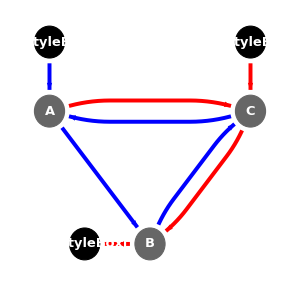
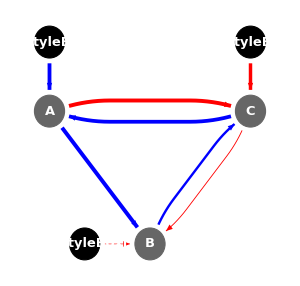
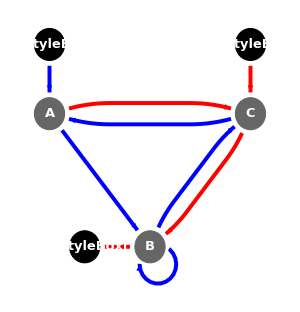
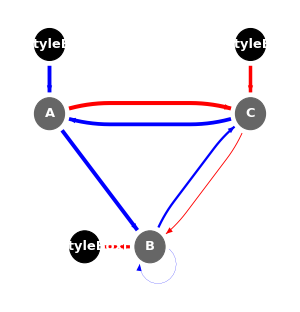
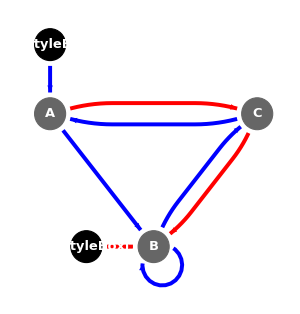
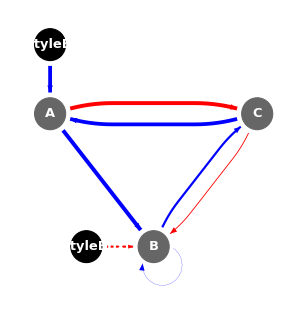
GRN Topology | GRN with interaction strength
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
tb=Table[{GraphGRN[grns[[i,1]]],GraphGRNInteractionStrength[grns[[i,1]]]},{i, Length[grns]}];
tb=Prepend[tb,{"GRN Topology","GRN with interaction strength"}];
Grid[tb, Frame->All]
```

#### Graph the GRN expression dynamics

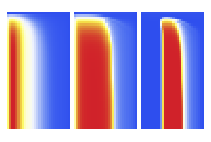

```mathematica
CreatSpaceTimePlots4GRC[
spatioTemporalExpressionProfile[grns[[2]]]
]
```

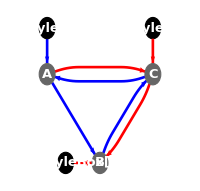
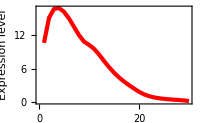
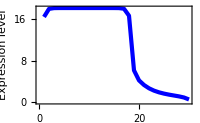
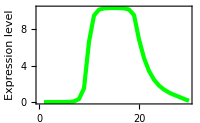
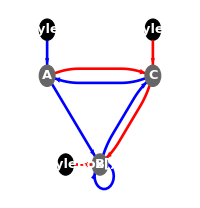
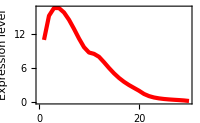
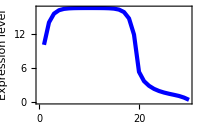
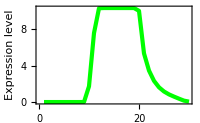

```mathematica
SolveGRCDynsBeforeAfterMorphInput[#][[{1,-1}]]&/@grns[[All]]
```